```mathematica
(* System Potential of continous logistic *)
Clear["Global`*"]
```

```mathematica
(* Define model as differential eqn. *)
dNdt=r N (1-N/K)(N/A-1)
```

N (-1+N/A) (1-N/K) r

```mathematica
(* Solve for equilibria *)
equil=Solve[dNdt==0,N];
%//TableForm
```

N→0
N→A
N→K

```mathematica
(* Specify some parameter values for plotting *)
parms={r->1,K->10,A->5};
```

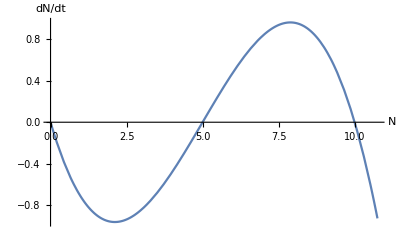

```mathematica
Plot[dNdt/.parms,{N,0,10.75},AxesLabel->{"N","dN/dt"}]
```

```mathematica
(* Derivative of dN/dt w.r.t. N*)
fDeriv=D[dNdt,N]//Expand
```

-r+(2 N r)/A+(2 N r)/K-(3 N^2 r)/(A K)

```mathematica
(* Evaluate first derivative at each equilibrium *)
fDeriv=fDeriv/.equil//Simplify;
TableForm[{{equil,fDeriv,fDeriv/.parms}}]
```

N→0
N→A
N→K | -r
r-(A r)/K
r-(K r)/A | -1
1/2
-1

```mathematica
(* System Potential *)
pN=-Integrate[dNdt,N]//Expand
```

(N^2 r)/2-(N^3 r)/(3 A)-(N^3 r)/(3 K)+(N^4 r)/(4 A K)

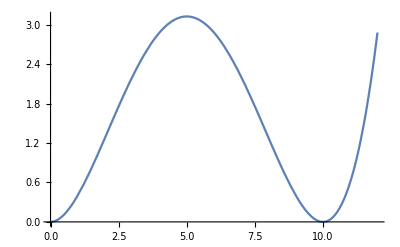

```mathematica
Plot[pN/.parms,{N,0,12}]
```